Autor: Krzysztof Barczak

# Metody numeryczne w technice

## (kierunek Matematyka)

## Projekt 3

Metoda Adamsa-Moultona

Napisać procedurę realizującą algorytm czterokrokowej metody Adamsa-Moultona (argumenty:  f, x_0, y_0, b, n, m).
Wykorzystać metodę iteracji prostej  (m powtórzeń), a jako metodę startową zastosować metodę Rungego-Kutty rzędy czwartego. Zminimalizować liczbę obliczeń funkcji   f.


Korzystając z napisanej procedury wyznaczyć rozwiązanie przybliżone zagadnienia początkowego:

{y'(x)=sin y(x),  x∈[0,25],
y(0)=1.

Obliczenia wykonać dla 10 i 20 kroków.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązania przybliżone.
Wykreślić także, na jednym rysunku, błędy uzyskanych rozwiązań przybliżonych.
Policzyć ponadto błędy maksymalne oraz średnie dla obu siatek.

## Rozwiązanie

### Metoda Rungego-Kutty rzędu czwartego - kod procedury

Wejście: 
	f = f(x,y) - funkcja;
	x0, y0 - wartości;
	n - liczba kroków;
	h - długość kroku.
Wyjście:
	(x_i,y_i) dla i=0,1,...,n - punkty.

```mathematica
Clear[metodaRK4];
metodaRK4[f_,x0_,y0_,h_,n_]:=Module[{yValues,xValues,xNext=x0,yNext=y0,k1,k2,k3,k4},

xValues={x0};
yValues={y0};

Do[
k1=f[xNext,yNext];
k2=f[xNext+h/2,yNext+(h k1)/2];
k3=f[xNext+h/2,yNext+(h k2)/2];
xNext=xNext+h;
xValues=Append[xValues,xNext];
k4=f[xNext,yNext+h k3];
yNext=yNext+1/6 h (k1+2 k2+2k3+k4);
yValues=Append[yValues,yNext],
{i,0,n-1}];

Return[Transpose[{xValues,yValues}]]
]
```

### Czterokrokowa metoda Adamsa-Moultona

Wejście:
	f - funkcja f(x,y),
	x0, y0 - wartości x_0,y_0,
	b - koniec przedziału,
	n - liczba kroków (n ≥ 4),
	m - liczba powtórzeń metody iteracji prostej.
Wyjście:
	(x_i,y_i) - punkty dla i=0,1,...,m.

```mathematica
Clear[metodaAM4];
metodaAM4[f_,x0_,y0_,b_,n_,m_]:=Module[{h=(b-x0)/n,xi,k=4,yi,fi,bki,temp},
xi=Table[x0+i h,{i,1,k-1}];
xi=Prepend[xi,x0];

yi=metodaRK4[f,x0,y0,h,k-1]⟦All,2⟧;

fi=Table[f[xi⟦i⟧,yi⟦i⟧],{i,1,k}];
fi=Prepend[fi,f[x0,y0]];

bki={251/720,646/720,-264/720,106/720,-19/720};

Do[
xi=Append[xi,xi⟦i-1⟧+h];
temp=yi[[i-1]];
(* Metoda iteracji prostej *)
Do[temp=yi[[i-1]]+h (∑_(j=2)^k bki⟦j⟧ fi⟦i+1-j⟧)+h bki[[1]]*f[xi[[i]],temp],m];
yi=Append[yi,temp];
fi=Append[fi,f[xi[[i]],yi[[i]]]],
{i,k+1,n+1}];

Return[Transpose[{xi,yi}]]
]
```

### Rozwiązanie zagadnienia początkowego

```mathematica
Clear[f,x0,y0,b,n,m,h];
f[x_,y_]:=Sin[y];
x0=0.;y0=1.;b=25.;n={10,20};m=20;h=(b-x0)/n;
przyblizone=Table[metodaAM4[f,x0,y0,b,i,m],{i,n}];

wykres10=ListPlot[przyblizone[[1]],PlotStyle->Orange,PlotRange->{1,4},PlotLegends->{"n=10"},PlotMarkers->{✶,Large}];
wykres20=ListPlot[przyblizone[[2]],PlotStyle->Brown,PlotRange->{1,4},PlotLegends->{"n=20"},PlotMarkers->{Automatic,Small}];
```

```mathematica
dsolve=DSolve[{y'[x]==f[x,y[x]],y[0]==1},y[x],x]⟦1,1,2⟧;
dokladneWykres=Plot[dsolve,{x,0,25},PlotStyle->{LightPink},PlotRange->All,PlotLegends->{"DSolve"}];
```

```mathematica
dokladne=Table[{x0+i h⟦j⟧,dsolve/.{x->x0+i h⟦j⟧}},{j,2},{i,0,n⟦j⟧}];

bledy=Table[{przyblizone[[j,i,1]],Abs[przyblizone[[j,i,2]]-dokladne[[j,i,2]]]},{j,2},{i,n[[j]]}];
maxBlad=Table[Max[bledy[[j,All,2]]],{j,2}];
avgBlad=Table[Mean[bledy[[j,All,2]]],{j,2}];

bledyWykres10=ListPlot[bledy[[1]],PlotStyle->Orange,PlotLegends->{"n=10"},Joined->True,PlotRange->All];
bledyWykres20=ListPlot[bledy[[2]],PlotStyle->Brown,PlotLegends->{"n=20"},Joined->True,PlotRange->All];
```

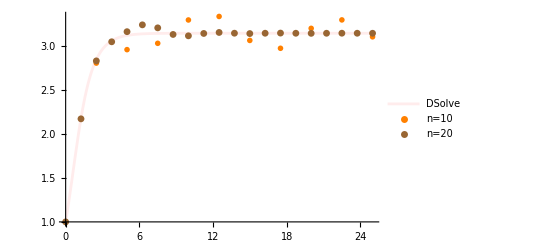

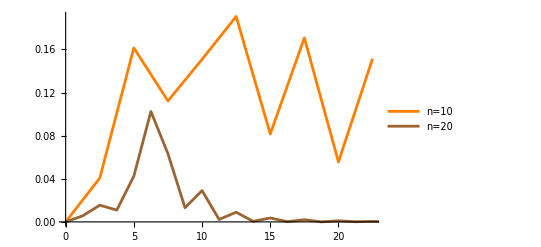

```mathematica
Show[dokladneWykres,wykres10,wykres20]
Show[bledyWykres10,bledyWykres20]
```

```mathematica
(* Maksymalne błędy dla odpowiednio n=10 i n=20 *)
maxBlad
```

{0.190589,0.10245}

```mathematica
(* Średnie błędy dla odpowiednio n=10 i n=20 *)
avgBlad
```

{0.111497,0.015083}